# Fig. 3

From “Schwarzschild-de Sitter spacetime in regular coordinates with cosmological time” (2025) by L. Lima and D.C. Rodrigues.

Davi C. Rodrigues

```mathematica
SetDirectory[NotebookDirectory[]];

$PlotTheme = {
  "Scientific", 
  "FrameGrid", 
  "BoldColor", 
  "SerifLabels", 
  "SizeScale", 
  {"BackgroundColor", White}
};

optionsPlot = {FrameStyle-> Directive[{Black, FontFamily -> "Times", FontSize -> 15}]};

Clear[Λ, m]
f[x_]= 1 - 2 m/x - Λ/3 x^2;

a[η_] = -(√3)/(√Λ η); (* a'>0 *)
```

## Negative f regions

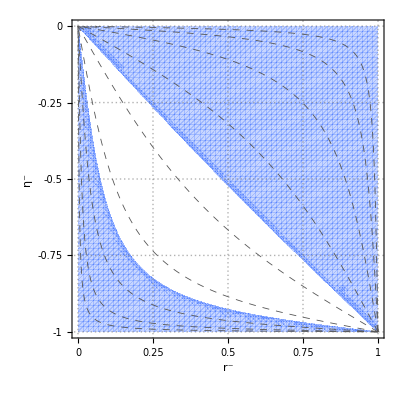

```mathematica
Λ = 10^-2;
m = 1;

ℓ[ηt_, rt_] = a[Tan[ηt π/2]] Tan[rt π/2];

frameticks = {
  {
    {{-1,-1,{0,0.02}},{-0.75,-0.75,{0,0.02}},{-0.5,-0.5,{0,0.02}}, {-0.25,-0.25,{0,0.02}}, {0,0,{0,0.02}}} (*left*), 
    None  (*right*)
  },
  {
    {{0,0,{0,0.02}},{0.25,0.25,{0,0.02}},{0.5,0.5,{0,0.02}}, {0.75,0.75,{0,0.02}}, {1.0,1,{0,0.02}}}, (*Bottom*)
    None (*top*) 
  }  
};

region = RegionPlot[
  {f[ℓ[ηt, rt]]< 0}, 
  {rt, 0, 1}, 
  {ηt, -1, 0}, 
  FrameStyle->Directive[12, Black],
  BoundaryStyle->None, 
  Evaluate@optionsPlot, 
  PlotPoints->60, 
  PlotRangePadding->None,
  FrameTicks -> frameticks
];

contour = ContourPlot[
  Evaluate@Table[a[Tan[ηt π/2]] Tan[rt π/2] == i, 
  {i, {10^-1, 10^-0.5, 1, 10^0.5, 10, 10^1.5, 10^2, 10^2.5, 10^3}}], 
  {rt, 0, 1}, 
  {ηt, -1, 0}, 
  Evaluate@optionsPlot, 
  ContourStyle-> Directive[Darker@Gray, Thickness[0.0015], Dashed],
  PlotPoints->50,
  MaxRecursion->4
];

show = Show[region, contour, FrameLabel-> {"r^-", "η^-"}]
```

## SdS: Outgoing geodesics

Outgoing light geodesics must satisfy

η'[r] = (A_+)^-1 = -1/ℓ^2 3/Λ A_- = 1/ℓ^2 3/Λ 1/2 (√(f[ℓ]^2 + 4 ℓ^2 Λ/3) - f[ℓ])

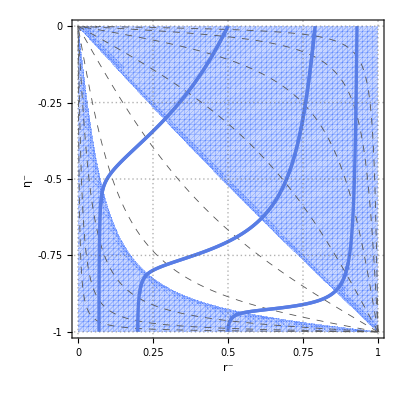

```mathematica
Clear[ηsol, η, ℓ, ℓsol, AmAbs, AmAbssol, ηprime, ηprimesol, rsolDomainMax, rsolMin, rsolMax, plotGeodesics];

ℓ[r_] = r a[η[r]];
ℓsol[η1_][r_] = r a[ηsol[η1][r]];

AmAbs[r_] = 1/2(Sqrt[f[ℓ[r]]^2 + 4 ℓ[r]^2 Λ/3] - f[ℓ[r]]); (*This is the absolute value of the negative A, A_-*)
AmAbssol[η1_][r_] = 1/2(Sqrt[f[ℓsol[η1][r]]^2 + 4 (ℓsol[η1][r])^2 Λ/3] - f[ℓsol[η1][r]]);

ηprime[r_] = 1/ℓ[r]^2 3/Λ AmAbs[r];
ηprimesol[η1_][r_] = 1/(ℓsol[η1][r])^2 3/Λ AmAbssol[η1][r];

ηsol[η1_?NumberQ] := ηsol[η1] =  Block[{},
  Off[NDSolveValue::precw];
  Off[NDSolveValue::ndsz];
  N @ NDSolveValue[
    {
      η'[r] == ηprime[r](*1/ℓ[r]^2 3/Λ AmAbs[r]*), 
      η[1] == η1
    }, η, {r, 0.1, 100}, 
    MaxStepSize -> 0.005, 
    MaxSteps -> Infinity, 
    WorkingPrecision->30, 
    PrecisionGoal -> 4, 
    AccuracyGoal -> ∞
  ] // Return;
  On[NDSolveValue::precw];
  On[NDSolveValue::ndsz];
];

rsolMin[η1_] := ηsol[η1]["Domain"][[1,1]]
rsolDomainMax[η1_] := rsolDomainMax[η1] = ηsol[η1]["Domain"][[1,2]]; 
rsolMax[η1_] := rsolMax[η1] = Block[{r}, 
  Min[
    rsolDomainMax[η1],
    r /. FindRoot[ηsol[η1][r] == 0, {r, Evaluate[rsolMin[η1] + 0.001], Evaluate[rsolDomainMax[η1]]}]
  ]
];

plotGeodesics[η1_] := plotGeodesics[η1] = Block[
  {rtMin, rtMax, tableArrowPositions, ff},
  rtMin = rt /. FindRoot[Tan[rt π/2] == rsolMin[η1], {rt, 0, 1}];
  rtMax = rt /. FindRoot[Tan[rt π/2] == rsolMax[η1], {rt, 0, 1}];
  ff[rt_] = 2/π ArcTan @ ηsol[η1][Tan[rt π/2]];
  Off[InterpolatingFunction::dprec];
  plotCurves = Plot[
    ff[rt], 
    {rt, rtMin, rtMax}, 
    PlotRange->All,
    PlotStyle->Thickness[0.006]
  ]; 
 tableArrowPositions = Table[{rt, ff[rt]}, {rt, rtMin, rtMax, 0.005}];
 listplotArrows = ListPlot[
   tableArrowPositions, 
   Joined -> True, 
   PlotStyle->Thickness[0.006]
 ] /. Line[x_] :> {Arrowheads[Table[.04, {3} (*Number of arrow heads*)]], Arrow[x]};
 Show[plotCurves, listplotArrows]
];

plotOut = Show[show, plotGeodesics[-10^-10], plotGeodesics[-2], plotGeodesics[-10^10]]
```

## SdS: Ingoing geodesics

Ingoing light geodesics must satisfy

η'[r] = - A_+ =  1/ℓ^2 3/Λ A_- = - 1/ℓ^2 3/Λ 1/2 (√(f[ℓ]^2 + 4 ℓ^2 Λ/3) - f[ℓ])

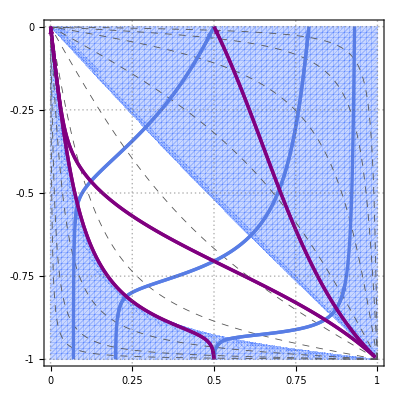

```mathematica
Clear[ηsol, η, ℓ, ℓsol, AmAbs, AmAbssol, ηprime, ηprimesol, rsolDomainMax, rsolMin, rsolMax, plotGeodesicsIn];

Λ = 10^-2;
m = 1;

ℓ[r_] = r a[η[r]];
ℓsol[η1_][r_] = r a[ηsol[η1][r]];

AmAbs[r_] = 1/2(Sqrt[f[ℓ[r]]^2 + 4 ℓ[r]^2 Λ/3] - f[ℓ[r]]);
AmAbssol[η1_][r_] = 1/2(Sqrt[f[ℓsol[η1][r]]^2 + 4 (ℓsol[η1][r])^2 Λ/3] - f[ℓsol[η1][r]]);

ηprime[r_] = - 1/ℓ[r]^2 3/Λ AmAbs[r];
ηprimesol[η1_][r_] = - 1/(ℓsol[η1][r])^2 3/Λ AmAbssol[η1][r];

ηsol[η1_?NumberQ] := ηsol[η1] =  Block[{},
  Off[NDSolveValue::precw];
  Off[NDSolveValue::ndsz];
  N @ NDSolveValue[
    {
      η'[r] == ηprime[r](*1/ℓ[r]^2 3/Λ AmAbs[r]*), 
      η[1] == η1
    }, η, {r, 1. 10^-10, 100}, 
    MaxStepSize -> 0.001, 
    MaxSteps -> Infinity, 
    WorkingPrecision->30, 
    PrecisionGoal -> 4, 
    AccuracyGoal -> ∞
  ] // Return;
  On[NDSolveValue::precw];
  On[NDSolveValue::ndsz];
];

rsolDomainMin[η1_] := ηsol[η1]["Domain"][[1,1]];
rsolDomainMax[η1_] := ηsol[η1]["Domain"][[1,2]]; 

rsolMax[η1_] := rsolDomainMax[η1];
rsolMin[η1_] := rsolMin[η1] = Block[{r}, 
  Max[
    rsolDomainMin[η1],
    Quiet[r /. FindRoot[ηsol[η1][r] == 0, {r, Evaluate[rsolDomainMin[η1]], Evaluate[rsolMax[η1] -  0.001]}]]
  ]
];

plotGeodesicsIn[η1_] := plotGeodesicsIn[η1] = Block[
  {rtMin, rtMax, tableArrowPositions, ff},
  rtMin = rt /. FindRoot[Tan[rt π/2] == rsolMin[η1], {rt, 0, 1}];
  rtMax = rt /. FindRoot[Tan[rt π/2] == rsolMax[η1], {rt, 0, 1}];
  ff[rt_] = 2/π ArcTan @ ηsol[η1][Tan[rt π/2]];
  Off[InterpolatingFunction::dprec];
  plotCurves = Plot[
    ff[rt], 
    {rt, rtMin, rtMax}, 
    PlotRange->All,
    PlotStyle->Directive[Thickness[0.006], Purple]
  ]; 
 tableArrowPositions = Reverse @ Table[{rt, ff[rt]}, {rt, rtMin, rtMax, 0.005}];
 listplotArrows = ListPlot[
   tableArrowPositions, 
   Joined -> True, 
   PlotStyle->Directive[Thickness[0.006], Purple]
 ] /. Line[x_] :> {Arrowheads[Table[.04, {3} (*Number of arrow heads*)]], Arrow[x]};
 Show[plotCurves, listplotArrows]
];

plotEtaRgeodesics = Show[plotOut, plotGeodesicsIn[-0.00001], plotGeodesicsIn[-2],plotGeodesicsIn[-10^5], FrameLabel-> {}]
```

```mathematica
Export["plotEtaRgeodesics.pdf", plotEtaRgeodesics]
```

plotEtaRgeodesics.pdf